### Drag Racer Solution

```mathematica
position[t_]:= Piecewise[{{0,t⩽5},{6(t-5)^2/2, t>5 && t<10}, {30(t-10) +75, t⩾10}}]
```

Here is a plot of what the drag racer is doing from t=3  to t=13.

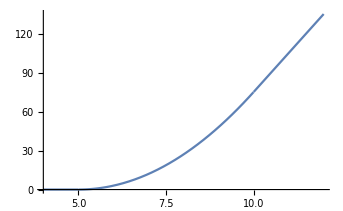

```mathematica
Plot[position[x],{x,4,12}]
```

Here is a table of the positions of the drag racer from t=4 to t=12.

```mathematica
tableOfValues=Table[{t, position[t], (position[t+0.5]- position[t])/0.5, ((position[t+1.0]-position[t+0.5])/0.5-(position[t+0.5]-position[t])/0.5)/0.5}, {t,4, 12, 0.5}];
```

```mathematica
Grid[Prepend[tableOfValues, {"time", "position", "   velocity   ", "acceleration"}], Frame->All]
```

time | position |    velocity    | acceleration
4. | 0 | 0. | 0.
4.5 | 0 | 0. | 3.
5. | 0 | 1.5 | 6.
5.5 | 0.75 | 4.5 | 6.
6. | 3. | 7.5 | 6.
6.5 | 6.75 | 10.5 | 6.
7. | 12. | 13.5 | 6.
7.5 | 18.75 | 16.5 | 6.
8. | 27. | 19.5 | 6.
8.5 | 36.75 | 22.5 | 6.
9. | 48. | 25.5 | 6.
9.5 | 60.75 | 28.5 | 3.
10. | 75. | 30. | 0.
10.5 | 90. | 30. | 0.
11. | 105. | 30. | 0.
11.5 | 120. | 30. | 0.
12. | 135. | 30. | 0.

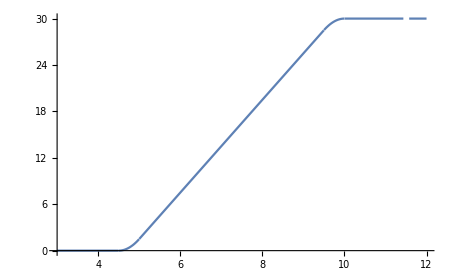

```mathematica
Plot[(position[t+0.5]-position[t])/0.5, {t, 3, 12}, PlotRange->{{3, 12},{0, 30}}]
```

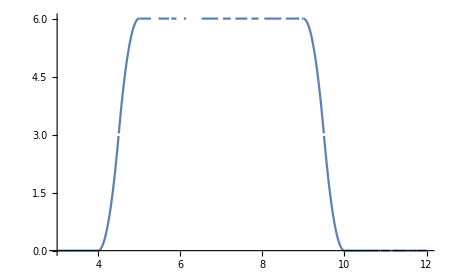

```mathematica
Plot[((position[t+1.0]-position[t+0.5])/0.5-(position[t+0.5]-position[t])/0.5)/0.5, {t, 3, 12}, PlotRange->{{3, 12},{0, 6}}]
```